## Customizing Functions

### Overview of Built-In function Properties

Syntax Coloring

```mathematica
Equal[a,b,
```

```mathematica
If[a,b,c,d,e]
```

```mathematica
If[a]
```

Optional Arguments

```mathematica
If[False,"true"]
```

```mathematica
If[False,"true","false"]
```

false

```mathematica
If[meh,"true","false","undecided"]
```

undecided

Options

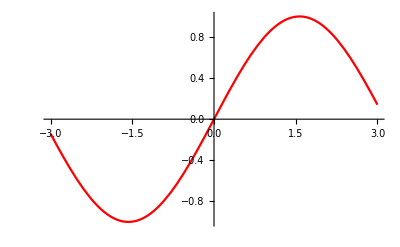

```mathematica
Plot[Sin[x],{x,-3,3},PlotStyle->Red]
```

Attributes

```mathematica
Attributes[Manipulate]
```

{HoldAll,Protected,ReadProtected}

Warning/Error Messages

```mathematica
5=x
```

Set::setraw: Cannot assign to raw object 5.

10

```mathematica
Set[5,x]
```

Set::setraw: Cannot assign to raw object 5.

10

```mathematica
Clear[x]
```

### Syntax Coloring

We can create Syntax Coloring properties for functions by using the

```mathematica
ClearAll[f]
SyntaxInformation[f]={"ArgumentsPattern"->{_,_}};
```

```mathematica
f[x]
```

```mathematica
f[x,y,z]
```

```mathematica
g[x_,y_]:=x+y
```

```mathematica
g[x,y,z]
```

g[x,y,z]

```mathematica
Remove[g,f]
```

### Optional and Default Arguments

The way we denote possible optional arguments is by using the  var_:default format when writting the parameters of the function

```mathematica
myStyle[x_,s_:10,e_:1]:=Framed[Style[x,s^e,Red]]
```

```mathematica
myStyle["Coco Bongo"]
```

Coco Bongo

```mathematica
myStyle["Coco Bongo",4]
```

Coco Bongo

```mathematica
myStyle["Coco Bongo",4,3]
```

Coco Bongo

### Options

```mathematica
ClearAll[f]
```

```mathematica
?f
```

```mathematica
Options[f]={color->Black}
```

{color→GrayLevel[0]}

```mathematica
?f
```

You can check the options using the Options function

```mathematica
Options[f]
```

{color→GrayLevel[0]}

```mathematica
Options[Manipulate]
```

{Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→None,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}

#### Defining the function with options

```mathematica
f[x_,OptionsPattern[]]:=Module[{a},
a=x^2;
Style[a,OptionValue[color]]
]
```

```mathematica
f[2]
```

4

```mathematica
f[2,color->Red]
```

4

#### Adding Syntax Coloring

```mathematica
ClearAll[f]
Options[f]={color->Red};
SyntaxInformation[f]={"ArgumentsPattern"->{_,OptionsPattern[]}};
```

```mathematica
f[x,color->Black,size->r]
```

```mathematica
Remove[f]
```

#### Warning

If color is defined somewhere else this could go wrong

```mathematica
Options[f]={color->Black};
```

```mathematica
color=7;
f[2,color->Red]
```

f[2,7→RGBColor[1, 0, 0]]

```mathematica
Clear[color]
```

```mathematica
f[2,color->Red]
```

4

### Attributes

Constant, Flat, HoldAll, HoldAllComplete, HoldFirst, HoldRest, Listable, Locked, NHoldAll,NHoldFirst, NHoldRest, NumericFunction,OneIdentity,Orderless, Protected, ReadProtected, SequenceHold, Stub, Temporary

```mathematica
TextGrid[Partition[{Constant,Flat,HoldAll,HoldAllComplete,HoldFirst,HoldRest,Listable,Locked,NHoldAll,NHoldFirst,NHoldRest,NumericFunction,OneIdentity,Orderless,Protected,ReadProtected,SequenceHold,Stub,Temporary},UpTo[5]],Frame->All]
```

Constant | Flat | HoldAll | HoldAllComplete | HoldFirst
HoldRest | Listable | Locked | NHoldAll | NHoldFirst
NHoldRest | NumericFunction | OneIdentity | Orderless | Protected
ReadProtected | SequenceHold | Stub | Temporary |

#### Constant

Constants always have derivative zero

```mathematica
Remove[f]
Attributes[f]={Constant};
```

```mathematica
D[f[x],x]
```

0

```mathematica
D[g[x],x]
```

g'[x]

```mathematica
Attributes[{π,ⅇ}]
```

{{Constant,Protected,ReadProtected},{Constant,Protected,ReadProtected}}

#### Flat

This is similar to giving the symbol the associative property

```mathematica
ClearAll[f]
Attributes[f]={Flat};
```

```mathematica
f[f[a,b],c]==f[a,f[b,c]]
```

True

```mathematica
g[g[a,b],c]==g[a,g[b,c]]
```

g[g[a,b],c]==g[a,g[b,c]]

#### HoldAll, HoldAllComplete, HoldFirst, HoldRest, NHoldAll,NHoldFirst, NHoldRest, SequenceHold

There are two types of evaluation of expressios in the Wolfrma Language, Standard and NonStandard
Standard evaluation of head[arg1,arg2,...,argn] is done by evaluating head then evaluating each argument followed by putting the whole expression together

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

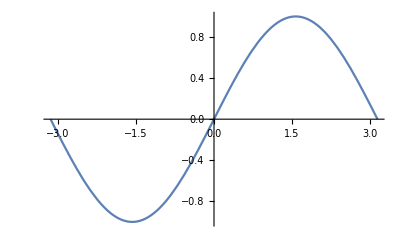

```mathematica
x=10;
Plot[Sin[x],{x,-π,π}]
```

```mathematica
Plot[Sin[10],{10,-π,π}]
```

$Failed

```mathematica
ClearAll[f];
Attributes[f]={HoldAll};
```

```mathematica
x=10
```

10

```mathematica
f[x_,y_]:=Plot[x,y]
```

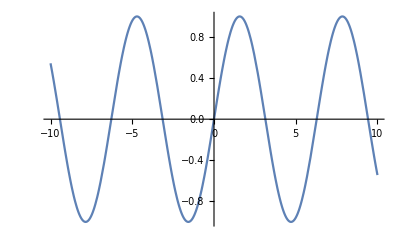

```mathematica
f[Sin[x],{x,-10,10}]
```

```mathematica
g[x_,y_]:=Plot[x,y]
```

```mathematica
g[Sin[x],{x,-10,10}]
```

$Failed

#### Listable

Listable gives you the ability to apply a function to the elements of a list

```mathematica
ClearAll[f]
SetAttributes[f,Listable]
```

```mathematica
f[{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
ClearAll[g]
```

```mathematica
g[{a,b,c}]
```

g[{a,b,c}]

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

```mathematica
f[head[a,b,c]]
```

f[head[a,b,c]]

```mathematica
f/@head[a,b,c]
```

head[f[a],f[b],f[c]]

```mathematica
f[{a,{b,c}}]
```

{f[a],{f[b],f[c]}}

```mathematica
g/@{a,{b,c}}
```

{g[a],g[{b,c}]}

#### Orderless

This attribute is similar to commutativity

```mathematica
ClearAll[f]
SetAttributes[f,Orderless]
```

```mathematica
f[a,b]==f[b,a]
```

True

```mathematica
g[a,b]==g[b,a]
```

g[a,b]==g[b,a]

#### Protected/ReadProtected

```mathematica
ClearAll[f]
SetAttributes[f,Protected]
```

```mathematica
f=5
```

Set::wrsym: Symbol f is Protected.

5

```mathematica
Clear[f]
```

Clear::wrsym: Symbol f is Protected.

```mathematica
Remove[f]
```

Remove::rmptc: Symbol f is Protected and cannot be removed.

```mathematica
Unprotect[f]
```

{f}

```mathematica
Remove[f]
```

### Error Messages

```mathematica
Length[a+b]
```

2

```mathematica
length[x_]:=If[Head[x]===List,Length[x],Message[length::list,x]]
```

```mathematica
length::usage = "length[x] calculates the length of x only if it is a list";
length::list="The input `1` is not a List";
```

```mathematica
?length
```

```mathematica
length[x]
```

```mathematica
length[{1,2,3}]
```

3

```mathematica
length[5]
```

length::list: The input 5 is not a List

### Exercises

Create a function that behaves like a mathematical set construct, that is it deletes duplicates and order of its elements does not matter. For example set[c,c,a,a,a,b] evaluates to set[a,b,c]

```mathematica
ClearAll[set]
```

```mathematica
Attributes[set]={Orderless}
```

```mathematica
set[a,b,c,c,c,c]
```

```mathematica
set[y___,x_,z___,x_,w___]:=set[x,y,z,w]
```

```mathematica
Union[set[a,b,c,d],set[a,g,c]]
```